```mathematica
"Henry Osei"
graphSlider[f_,a_,lb_,ub_]:=DynamicModule[{g,x},
g[x_]=f[x];
Manipulate[Plot[g[x],{x,lb,ub},Exclusions->{a},
Epilog->{PointSize[Large],Point[{pta,g[pta]}],
Dashed,Line[{{pta,0},{pta,g[pta]},{0,g[pta]}}]}],{{pta,(a+ub)/2,"x"},lb,ub}]
]
Clear[f]
f[x_] := (x^2 + 1)/(x-1)
graphSlider[f,1,0,2]
```

```mathematica
Clear [f]
f[x_]:=Cos[1/x] 
graphSlider [f,0,-1,1]
```

```mathematica
Clear [f]
f[x_]:=x Sin[1/x] 
graphSlider [f,0,-1,1]
```

```mathematica
Clear[f]
f[x_] := (x^2 - 1)/(x-2)
graphSlider[f,2,0,4]
```

```mathematica
Clear[f]
f[x_] := (1)/(1+Exp[1/x])
graphSlider[f,0,-1,1]
```

```mathematica
Clear[f]
f[x_] := (Log[x])/(x+1)
graphSlider[f,-1,-2,2]
```

```mathematica
epsilonDelta[g_,a_,L_]:=Module[{x,f,x0,y0},f[x_]=g[x];x0=a;y0=L;
Manipulate[
GraphicsRow[
{Plot[f[x],{x,x0-delta,x0+delta},PlotRange->{y0-eps,y0+eps},ImagePadding->15,ImageSize->300],
Show[{Plot[f[x],{x,x0-0.6,x0+0.6},PlotRange->{y0-0.6,y0+0.6},ImageSize->300],
Graphics[{{Red,Line[{{x0-0.65,y0-eps},{x0+0.65,y0-eps}, {x0+0.65,y0+eps},{x0-0.65,y0+eps}}]},
{Red,Line[{{x0-delta,y0-0.65},{x0-delta,y0+0.65},{x0+delta,y0+0.65},{x0+delta,y0-0.65}}]}}]}]}],
{{eps,0.5,"ϵ"},0.5,10^(-7)},{{delta,0.5,"δ"},0.5,10^(-7)},LabelStyle->Medium]
]
Clear[f]
f[x_]:=Abs[x-2]/(x-2)
epsilonDelta[f,2,0]
```

General::prng: Value of option PlotRange -> {-0.5+y0$23504,0.5+y0$23504} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Plot::plln: Limiting value -0.5+x0$23504 in {x$23504,x0$23504-FE`delta$$33,x0$23504+FE`delta$$33} is not a machine-sized real number.

General::prng: Value of option PlotRange -> {-0.6+y0$23504,0.6+y0$23504} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Plot::plln: Limiting value -0.6+x0$23504 in {x$23504,x0$23504-0.6,x0$23504+0.6} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[f$23504[x$23504],{x$23504,x0$23504-0.6,x0$23504+0.6},PlotRange→{y0$23504-0.6,y0$23504+0.6},ImageSize→300],}].

General::prng: Value of option PlotRange -> {-0.5+y0$23504,0.5+y0$23504} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

Plot::plln: Limiting value -0.5+x0$23504 in {x$23504,x0$23504-FE`delta$$33,x0$23504+FE`delta$$33} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[f$23504[x$23504],{x$23504,x0$23504-0.6,x0$23504+0.6},PlotRange→{y0$23504-0.6,y0$23504+0.6},ImageSize→300],}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Not continuous because the graph does not stay in the box.

```mathematica
Clear[f]
f[x_]:=x Sin[1/x]
epsilonDelta[f,0,0]
```

General::prng: Value of option PlotRange -> {-0.5+y0$67236,0.5+y0$67236} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Plot::plln: Limiting value -0.5+x0$67236 in {x$67236,x0$67236-FE`delta$$36,x0$67236+FE`delta$$36} is not a machine-sized real number.

General::prng: Value of option PlotRange -> {-0.6+y0$67236,0.6+y0$67236} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Plot::plln: Limiting value -0.6+x0$67236 in {x$67236,x0$67236-0.6,x0$67236+0.6} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[f$67236[x$67236],{x$67236,x0$67236-0.6,x0$67236+0.6},PlotRange→{y0$67236-0.6,y0$67236+0.6},ImageSize→300],}].

General::prng: Value of option PlotRange -> {-0.5+y0$67236,0.5+y0$67236} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

Plot::plln: Limiting value -0.5+x0$67236 in {x$67236,x0$67236-FE`delta$$36,x0$67236+FE`delta$$36} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[f$67236[x$67236],{x$67236,x0$67236-0.6,x0$67236+0.6},PlotRange→{y0$67236-0.6,y0$67236+0.6},ImageSize→300],}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

As the epsion approches x, the graph gets more vertically narrow. As the delta approches x, the graph gets more horizontally wider.

```mathematica
Clear[f]
f[x_]:=Sin[Tan [x/2]]
epsilonDelta[f,Pi,3/4]
```

General::prng: Value of option PlotRange -> {-0.5+y0$78748,0.5+y0$78748} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Plot::plln: Limiting value -0.5+x0$78748 in {x$78748,x0$78748-FE`delta$$39,x0$78748+FE`delta$$39} is not a machine-sized real number.

General::prng: Value of option PlotRange -> {-0.6+y0$78748,0.6+y0$78748} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Plot::plln: Limiting value -0.6+x0$78748 in {x$78748,x0$78748-0.6,x0$78748+0.6} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[f$78748[x$78748],{x$78748,x0$78748-0.6,x0$78748+0.6},PlotRange→{y0$78748-0.6,y0$78748+0.6},ImageSize→300],}].

General::prng: Value of option PlotRange -> {-0.5+y0$78748,0.5+y0$78748} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

Plot::plln: Limiting value -0.5+x0$78748 in {x$78748,x0$78748-FE`delta$$39,x0$78748+FE`delta$$39} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[f$78748[x$78748],{x$78748,x0$78748-0.6,x0$78748+0.6},PlotRange→{y0$78748-0.6,y0$78748+0.6},ImageSize→300],}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

```mathematica
As the epsion approches x, the graph gets more vertically narrow. As the delta approches x, the graph gets more horizontally wider.
```

```mathematica
Clear[f]
f[x_]:=Abs[x]
epsilonDelta[f,0,0]
```

As the epsion approches x, the graph gets more vertically narrow. As the delta approches x, the graph gets more horizontally wider.

```mathematica
Clear[f]
f[x_]:=Sin[x]/(x)
epsilonDelta[f,-2,0]
```

Not continuous. Y value never gets inside box.

```mathematica
Limit[Sin[x]/x, x->0, Direction ->-1]
```

1

```mathematica
Limit[Sin[x]/x, x->0, Direction ->1]
```

1

```mathematica
Limit[Sin[x]-x/x^3, x->0, Direction ->-1]
```

-∞

```mathematica
Limit[Sin[x]-x/x^3, x->0, Direction ->1]
```

-∞

```mathematica
Limit [(1+1)/(x)^x, x->0, Direction ->1]
```

2

```mathematica
Limit[(x-1)/Sqrt[x]-1, x->1, Direction ->1]
```

-1

```mathematica
Limit[Cos[x]-1/x, x->0, Direction ->-1]
```

-∞

```mathematica
Limit[Cos[x]-1/x, x->0, Direction ->1]
```

∞

```mathematica
Limit[Sin[x]-x+x^3/6/x^5, x->0, Direction ->-1]
```

∞

```mathematica
Limit[Sin[x]-x+x^3/6/x^5, x->0, Direction ->1]
```

∞

```mathematica
Limit[(1+Sin[x]^1)/x, x->0, Direction ->1]
```

-∞

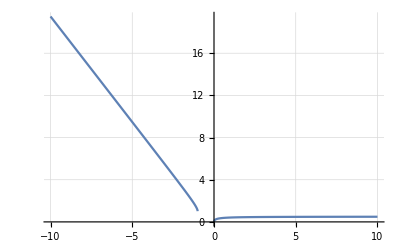

```mathematica
Clear[f]
f[x_]:= Sqrt[x^2+x]-x
Plot[f[x], {x,-10,10}, GridLines -> Automatic]
```

The horizontal asymptote is x=-1.

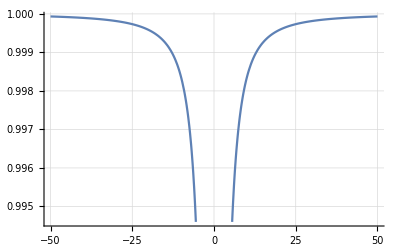

```mathematica
Clear[g]
g[x_]:= x Sin[1/x]
Plot[g[x], {x,-50,50}, GridLines -> Automatic]
```

The horizontal asymptote is x=0.